```mathematica
SetOptions[EvaluationNotebook[],StyleHints->{"CodeFont"->"Courier"}]
```

Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

Fourier-Legendre Series
Showing the details, develop:

1. 63x^5 -90 x^3 + 35x

```mathematica
Clear["Global`*"]
```

```mathematica
fp[x_]=63 x^5-90 x^3+35 x
```

35 x-90 x^3+63 x^5

```mathematica
FourierLegendreA[f_,x_,n_]:=(2n+1)/2Integrate[LegendreP[n,x]f,{x,-1,1}]
```

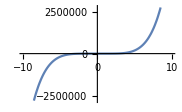

```mathematica
Plot[fp[x],{x,-10,10}]
```

```mathematica
Factor[Table[FourierLegendreA[63 x^5 -90 x^3+35 x ,x,n],{n,0,7}]]
```

{0,8,0,-8,0,8,0,0}

The green cell above agrees with the answer in the text (showing non-zero coefficients at P_1,P_3, and P_5). The FLA function was found on Eric Weisstein’s Math World. The s.m. points out that the reason the odd coefficients are non-zero is that the function is odd.

3. 1 - x^4

```mathematica
fg[x]=1 - x^4
```

1-x^4

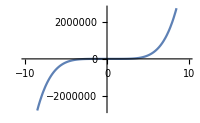

```mathematica
Plot[fp[x],{x,-10,10}, ImageSize->200
]
```

```mathematica
Factor[Table[FourierLegendreA[1-x^4 ,x,n],{n,0,7}]]
```

{4/5,0,-4/7,0,-8/35,0,0,0}

The answer above matches that of the text.

8 -- 13 Fourier-Legendre Series
Find and graph (on common axes) the partial sums up to S_m_0 whose graph practically coincides with that of f(x) within graphical accuracy. State m_0. On what does the size of m_0 seem to depend?

9. f(x) = sin 2πx

```mathematica
N[Factor[Table[FourierLegendreA[Sin[2 π x] ,x,n],{n,0,7}]]]
```

{0.,-0.477465,0.,-0.690783,0.,1.8441,0.,-0.823621}

The above coefficients match the values in the text.

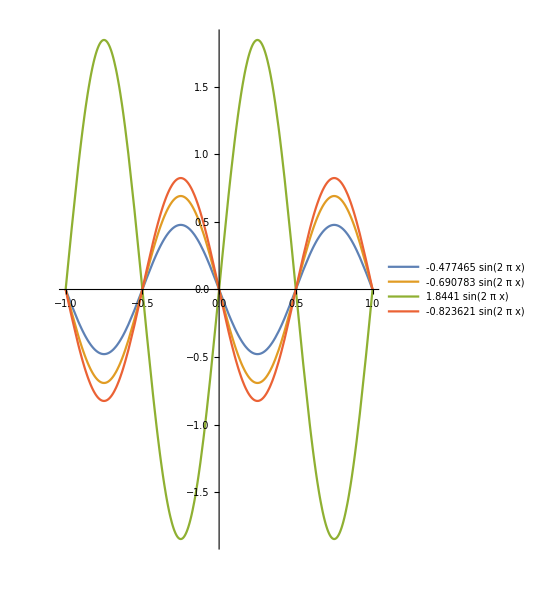

```mathematica
Plot[{{-0.477464829275686Sin[2π x]},{-0.6907832122075241Sin[2 π x]},{1.8440983138592046Sin[2 π x]},{-0.8236205222550245Sin[2 π x]}},{x,-1,1},AspectRatio->3/2,PlotLegends->"Expressions"]
```

The above plot resembles that in the s.m., but not closely. As far as m_0 goes, I don’t know how to establish it.  Logically, even functions would have m_0 of zero, and odd functions have m_0 of one. But the question above implies it could be sizable. I couldn’t find a place in either text or s.m. which gave the answer; they both coyly asked the student what it was. In the above functions, the order is: teal, orange, green, red.

11. f(x) = (1 + x^2)^-1

```mathematica
Clear["Global`*"]
```

```mathematica
FourierLegendreA[f_,x_,n_]:=(2n+1)/2Integrate[LegendreP[n,x]f,{x,-1,1}]
```

```mathematica
fh[x_] = (1+x^2)^-1
```

1/(1+x^2)

```mathematica
N[Factor[Table[FourierLegendreA[fh[x] ,x,n],{n,0,7}]]]
```

{0.785398,0.,-0.353982,0.,0.0829595,0.,-0.0172211,0.}

The above coefficients match the values in the text.

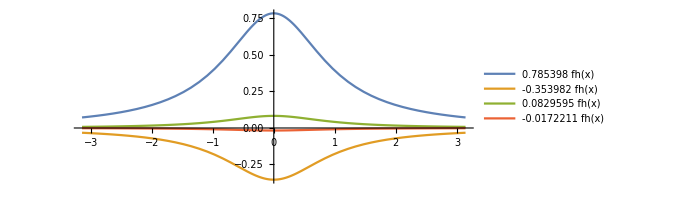

```mathematica
Plot[{{0.7853981633974483fh[x]},{-0.3539816339744828fh[x]},{0.08295949990479201fh[x]},{-0.017221090839916544fh[x]}},{x,-π,π}, AspectRatio->Automatic, PlotRange->Full,PlotLegends->"Expressions"]
```

The color order is the same as the last problem.

13. f(x) = Subscript[J, 0](α_(0,2)x),   a_(0,2) =the second positive zero of J_0(x)

I don’t understand this problem.